## Lab. di Dinamica dei Veicoli

### Import Data

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\Antonio\Desktop\Laboratorio di Dinamica dei Veicoli\Progetto

```mathematica
parameters=ChoiceDialog["Please select the car parameters",
FileNames["Car_Parameters/*.json"]]
```

Car_Parameters\test.json

```mathematica
data=ToExpression[TextString[Import[parameters,"JSON"]]];
```

```mathematica
dataG={
l->a1+a2,
μ->mu,
qb->((a2*q1+a1*q2)/(a1+a2)),
δ10->delta10*(Pi/180),
δ20->delta20*(Pi/180),
τ1->tau1,τ2->tau2,
ϵ1->epsilon1,ϵ2->epsilon2,
ρ->rho,
kϕ1->kphi1,kϕ2->kphi2,
kϕ->kphi1+kphi2,
kϕ1p->kphi1p,kϕ2p->kphi2p,
kϕp->kphi1p+kphi2p,
kϕ1s->kphi1s,kϕ2s->kphi2s,
kϕs->kphi1s+kphi2s,
Jz->m*a1*a2*0.92
}/.data;
```

```mathematica
traction=ToString@Extract[Association[data],Key@Traction]
```

rear

```mathematica
keyList ={{Key@delta10},{Key@delta20},
{Key@tau1},{Key@tau2},{Key@epsilon1},
{Key@epsilon2},{Key@rho},{Key@kphi1},
{Key@kphi2},{Key@kphi1p},{Key@kphi2p},
{Key@Traction},{Key@kphi1s},{Key@kphi2s}};
```

```mathematica
param=Normal@Thread[Delete[Association[Join[data,dataG]],keyList]]
```

{m→1464,g→9.81,a1→1.13,a2→1.47,t1→1.6,t2→1.6,h→0.55,rr1→0.25,rr2→0.25,mu→1.4,a1mf→-0.00005,a2mf→1,a3mf→55000,a4mf→4000,ya→0.8,xm→0.08,Sa→2,Cx→0.35,Cz1→0.,Cz2→0.,Jzx→10,q1→0.05,q2→0.05,k1→31500,k2→28000,c1→2948.4,c2→2620.8,l→2.6,μ→1.4,qb→0.05,δ10→0.,δ20→0.,τ1→0.05,τ2→0.,ϵ1→1.,ϵ2→0.,ρ→1.225,kϕ1→50000,kϕ2→40000,kϕ→90000,kϕ1p→400,kϕ2p→500,kϕp→900,kϕ1s→21740.6,kϕ2s→22322.2,kϕs→44062.8,Jz→2237.3}

#### Colors

```mathematica
ColorData[97, "ColorList"]
```

{RGBColor[0.368417, 0.506779, 0.709798],RGBColor[0.880722, 0.611041, 0.142051],RGBColor[0.560181, 0.691569, 0.194885],RGBColor[0.922526, 0.385626, 0.209179],RGBColor[0.528488, 0.470624, 0.701351],RGBColor[0.772079, 0.431554, 0.102387],RGBColor[0.363898, 0.618501, 0.782349],RGBColor[1, 0.75, 0],RGBColor[0.647624, 0.37816, 0.614037],RGBColor[0.571589, 0.586483, 0.],RGBColor[0.915, 0.3325, 0.2125],RGBColor[0.40082222609352647, 0.5220066643438841, 0.85],RGBColor[0.9728288904374106, 0.621644452187053, 0.07336199581899142],RGBColor[0.736782672705901, 0.358, 0.5030266573755369],RGBColor[0.28026441037696703, 0.715, 0.4292089322474965]}

```mathematica
orange = ColorData[97, "ColorList"][[2]]
```

RGBColor[0.880722, 0.611041, 0.142051]

```mathematica
red = ColorData[3, "ColorList"][[2]]
```

RGBColor[0.996078431372549, 0.3607843137254902, 0.027450980392156862]

```mathematica
blue = ColorData[97, "ColorList"][[1]]
```

RGBColor[0.368417, 0.506779, 0.709798]

```mathematica
green = ColorData[97, "ColorList"][[3]]
```

RGBColor[0.560181, 0.691569, 0.194885]

### Equations

#### Accelerations

```mathematica
ax[udot_,v_,r_]:=udot-v*r;
```

```mathematica
ay[vdot_,u_,r_]:=vdot+u*r;
```

```mathematica
Y[vdot_,u_,r_]:=m*ay[vdot,u,r];
```

```mathematica
Y1[vdot_,u_,r_]:=m*ay[vdot,u,r]*(a2/l);
```

```mathematica
Y2[vdot_,u_,r_]:=m*ay[vdot,u,r]*(a1/l);
```

#### Steer Angles

```mathematica
δFunc[δv_,δ0_,τ_,ϵ_,t_,j_]:=
(-1)^j*δ0+τ*δv+(-1)^(j+1)*ϵ*((t)/(2*l))*(τ*δv)^2;
```

```mathematica
δ11[δv_]:=δFunc[δv,δ10,τ1,ϵ1,t1,1];
```

```mathematica
δ12[δv_]:=δFunc[δv,δ10,τ1,ϵ1,t1,2];
```

```mathematica
δ21[δv_]:=δFunc[δv,δ20,τ2,ϵ2,t2,1];
```

```mathematica
δ22[δv_]:=δFunc[δv,δ20,τ2,ϵ2,t2,2];
```

#### Velocity of the wheels (body frame)

```mathematica
Vijb[u_,v_,r_,ti_,ai_,i_,j_]:=
{u+(-1)^j*(r*ti/2)/1,v-(-1)^i*r*1*ai};
```

```mathematica
V11b[u_,v_,r_]:=Vijb[u,v,r,t1,a1,1,1];
```

```mathematica
V12b[u_,v_,r_]:=Vijb[u,v,r,t1,a1,1,2];
```

```mathematica
V21b[u_,v_,r_]:=Vijb[u,v,r,t2,a2,2,1];
```

```mathematica
V22b[u_,v_,r_]:=Vijb[u,v,r,t2,a2,2,2];
```

#### Velocity of the wheels (wheels frame)

Matrice di rotazione che mi porta da wheel a body

```mathematica
Rbw[δij_]:={{Cos[δij], -Sin[δij]},
		      {Sin[δij],   Cos[δij]}};
```

```mathematica
V11w[u_,v_,r_,δv_]:=Transpose[Rbw[δ11[δv]]].V11b[u,v,r];
```

```mathematica
V12w[u_,v_,r_,δv_]:=Transpose[Rbw[δ12[δv]]].V12b[u,v,r];
```

```mathematica
V21w[u_,v_,r_,δv_]:=Transpose[Rbw[δ21[δv]]].V21b[u,v,r];
```

```mathematica
V22w[u_,v_,r_,δv_]:=Transpose[Rbw[δ22[δv]]].V22b[u,v,r];
```

#### Longitudinal Slips

```mathematica
σx11[u_,v_,r_,ω11_,δv_]:=(V11w[u,v,r,δv][[1]]-ω11*rr1)/(ω11*rr1);
```

```mathematica
σx12[u_,v_,r_,ω12_,δv_]:=(V12w[u,v,r,δv][[1]]-ω12*rr1)/(ω12*rr1);
```

```mathematica
σx21[u_,v_,r_,ω21_,δv_]:=(V21w[u,v,r,δv][[1]]-ω21*rr2)/(ω21*rr2);
```

```mathematica
σx22[u_,v_,r_,ω22_,δv_]:=(V22w[u,v,r,δv][[1]]-ω22*rr2)/(ω22*rr2);
```

#### Lateral Slips

```mathematica
σy11[u_,v_,r_,ω11_,δv_]:=(V11w[u,v,r,δv][[2]])/(ω11*rr1);
```

```mathematica
σy12[u_,v_,r_,ω12_,δv_]:=(V12w[u,v,r,δv][[2]])/(ω12*rr1);
```

```mathematica
σy21[u_,v_,r_,ω21_,δv_]:=(V21w[u,v,r,δv][[2]])/(ω21*rr2);
```

```mathematica
σy22[u_,v_,r_,ω22_,δv_]:=(V22w[u,v,r,δv][[2]])/(ω22*rr2);
```

#### Total Slips

```mathematica
σ11[u_,v_,r_,ω11_,δv_]:=Sqrt[σx11[u,v,r,ω11,δv]^2+σy11[u,v,r,ω11,δv]^2];
```

```mathematica
σ12[u_,v_,r_,ω12_,δv_]:=Sqrt[σx12[u,v,r,ω12,δv]^2+σy12[u,v,r,ω12,δv]^2];
```

```mathematica
σ21[u_,v_,r_,ω21_,δv_]:=Sqrt[σx21[u,v,r,ω21,δv]^2+σy21[u,v,r,ω21,δv]^2];
```

```mathematica
σ22[u_,v_,r_,ω22_,δv_]:=Sqrt[σx22[u,v,r,ω22,δv]^2+σy22[u,v,r,ω22,δv]^2];
```

#### Magic Formula

```mathematica
Dmf[Fz_]:=(a1mf*Fz+a2mf)*Fz;
```

```mathematica
Cmf[Fz_]:=2-(2/Pi)*ArcSin[ya/Dmf[Fz]];
```

```mathematica
Bmf[Fz_]=(a3mf*Sin[2*ArcTan[(Fz/a4mf)]])/(Cmf[Fz]*Dmf[Fz]);
```

```mathematica
Emf[Fz_]:=(Bmf[Fz]*xm-Tan[Pi/(2*Cmf[Fz])])   /   (Bmf[Fz]*xm-ArcTan[Bmf[Fz]]*xm);
```

```mathematica
Ft[σ_,Fz_]:=
Dmf[Fz]*Sin[Cmf[Fz]*ArcTan[Bmf[Fz]*σ-Emf[Fz](Bmf[Fz]*σ-ArcTan[Bmf[Fz]*σ])]];
```

```mathematica
Manipulate[
Plot[{Ft[σ,Fz]/.param},{σ,0,0.6},
PlotRange->{All,{0,5000}},AspectRatio->1/2.4,
PlotLabel->"Magic Formula",ImageSize->600,LabelStyle->Directive[Bold,11],
Frame->True, RotateLabel->False,PlotStyle->{green,Thick},
FrameLabel->{HoldForm["σ"], HoldForm["Ft"]},Filling->Automatic,
GridLines->Automatic, GridLinesStyle->{{Gray, Dotted}, {Gray, Dotted}}],
{Fz,2000,5000}]
```

```mathematica
Manipulate[
Plot[Dm*Sin[Cm*ArcTan[Bm*x-Em*(Bm*x-ArcTan[Bm*x])]],{x,0,1},
PlotRange->{All,{0,10}},PlotTheme->"Scientific",
AspectRatio->1/2.3,ImageSize->500,
FrameLabel->{HoldForm["x"], HoldForm["y"]},
LabelStyle->Directive[15],
GridLines->Automatic],
{Dm,6,10},{Cm,1,2},{Bm,5,10},{Em,-1,1}
]
```

#### Static Loads

```mathematica
Z10=(m*g*a2)/l;
```

```mathematica
Z20=(m*g*a1)/l;
```

#### Aerodinamic Forces

```mathematica
ζ=(1/2)*ρ*Sa*Cx;
```

```mathematica
ξ1=(1/2)*ρ*Sa*Cz1;
```

```mathematica
ξ2=(1/2)*ρ*Sa*Cz2;
```

```mathematica
Xa[u_]:=ζ*u^2;
```

```mathematica
Z1a[u_]:=ξ1*u^2;
```

```mathematica
Z2a[u_]:=ξ2*u^2;
```

#### Load Transfers

```mathematica
ΔZ[udot_,v_,r_]:=-(m*ax[udot,v,r]*h+Jzx*r^2)/l;
```

```mathematica
ΔZ1[vdot_,u_,r_]:=
(1/t1)*((kϕ1/kϕ)*Y[vdot,u,r]*(h-qb)+Y1[vdot,u,r]*q1+((kϕ1*kϕ2)/kϕ)*((Y2[vdot,u,r]*q2)/(kϕ2p)-(Y1[vdot,u,r]*q1)/(kϕ1p)));
```

```mathematica
ΔZ2[vdot_,u_,r_]:=
(1/t2)*((kϕ2/kϕ)*m*ay[vdot,u,r]*(h-qb)+Y2[vdot,u,r]*q2+((kϕ1*kϕ2)/kϕ)*((Y1[vdot,u,r]*q1)/(kϕ1p)-(Y2[vdot,u,r]*q2)/(kϕ2p)));
```

#### Vertical Forces to the axles

```mathematica
Z1[u_,udot_,v_,r_]:=Z10+Z1a[u]+ΔZ[udot,v,r];
```

```mathematica
Z2[u_,udot_,v_,r_]:=Z20+Z2a[u]-ΔZ[udot,v,r];
```

#### Vertical Forces to the wheels

```mathematica
Z11[u_,udot_,v_,r_,vdot_]:=
(1/2)*(Z10+Z1a[u]+ΔZ[udot,v,r])-ΔZ1[vdot,u,r];
```

```mathematica
Z12[u_,udot_,v_,r_,vdot_]:=
(1/2)*(Z10+Z1a[u]+ΔZ[udot,v,r])+ΔZ1[vdot,u,r];
```

```mathematica
Z21[u_,udot_,v_,r_,vdot_]:=
(1/2)*(Z20+Z2a[u]-ΔZ[udot,v,r])-ΔZ2[vdot,u,r];
```

```mathematica
Z22[u_,udot_,v_,r_,vdot_]:=
(1/2)*(Z20+Z2a[u]-ΔZ[udot,v,r])+ΔZ2[vdot,u,r];
```

#### Forces to the wheels (wheel frame)

Forze longitudinali

```mathematica
Fx11[u_,v_,r_,ω11_,udot_,vdot_,δv_]:=
-(σx11[u,v,r,ω11,δv]/σ11[u,v,r,ω11,δv])*Ft[σ11[u,v,r,ω11,δv],Z11[u,udot,v,r,vdot]];
```

```mathematica
Fx12[u_,v_,r_,ω12_,udot_,vdot_,δv_]:=
-(σx12[u,v,r,ω12,δv]/σ12[u,v,r,ω12,δv])*Ft[σ12[u,v,r,ω12,δv],Z12[u,udot,v,r,vdot]];
```

```mathematica
Fx21[u_,v_,r_,ω21_,udot_,vdot_,δv_]:=
-(σx21[u,v,r,ω21,δv]/σ21[u,v,r,ω21,δv])*Ft[σ21[u,v,r,ω21,δv],Z21[u,udot,v,r,vdot]];
```

```mathematica
Fx22[u_,v_,r_,ω22_,udot_,vdot_,δv_]:=
-(σx22[u,v,r,ω22,δv]/σ22[u,v,r,ω22,δv])*Ft[σ22[u,v,r,ω22,δv],Z22[u,udot,v,r,vdot]];
```

Forze laterali

```mathematica
Fy11[u_,v_,r_,ω11_,udot_,vdot_,δv_]:=
-(σy11[u,v,r,ω11,δv]/σ11[u,v,r,ω11,δv])*Ft[σ11[u,v,r,ω11,δv],Z11[u,udot,v,r,vdot]];
```

```mathematica
Fy12[u_,v_,r_,ω12_,udot_,vdot_,δv_]:=
-(σy12[u,v,r,ω12,δv]/σ12[u,v,r,ω12,δv])*Ft[σ12[u,v,r,ω12,δv],Z12[u,udot,v,r,vdot]];
```

```mathematica
Fy21[u_,v_,r_,ω21_,udot_,vdot_,δv_]:=
-(σy21[u,v,r,ω21,δv]/σ21[u,v,r,ω21,δv])*Ft[σ21[u,v,r,ω21,δv],Z21[u,udot,v,r,vdot]];
```

```mathematica
Fy22[u_,v_,r_,ω22_,udot_,vdot_,δv_]:=
-(σy22[u,v,r,ω22,δv]/σ22[u,v,r,ω22,δv])*Ft[σ22[u,v,r,ω22,δv],Z22[u,udot,v,r,vdot]];
```

#### Force to the wheels (body frame)

```mathematica
XY11[u_,v_,r_,δv_,ω11_,udot_,vdot_]:=
Rbw[δ11[δv]].{Fx11[u,v,r,ω11,udot,vdot,δv],Fy11[u,v,r,ω11,udot,vdot,δv]};
```

```mathematica
XY12[u_,v_,r_,δv_,ω12_,udot_,vdot_]:=
Rbw[δ12[δv]].{Fx12[u,v,r,ω12,udot,vdot,δv],Fy12[u,v,r,ω12,udot,vdot,δv]};
```

```mathematica
XY21[u_,v_,r_,δv_,ω21_,udot_,vdot_]:=
Rbw[δ21[δv]].{Fx21[u,v,r,ω21,udot,vdot,δv],Fy21[u,v,r,ω21,udot,vdot,δv]};
```

```mathematica
XY22[u_,v_,r_,δv_,ω22_,udot_,vdot_]:=
Rbw[δ22[δv]].{Fx22[u,v,r,ω22,udot,vdot,δv],Fy22[u,v,r,ω22,udot,vdot,δv]};
```

```mathematica
X11[u_,v_,r_,δv_,ω11_,udot_,vdot_]:=XY11[u,v,r,δv,ω11,udot,vdot][[1]];
```

```mathematica
X12[u_,v_,r_,δv_,ω12_,udot_,vdot_]:=XY12[u,v,r,δv,ω12,udot,vdot][[1]];
```

```mathematica
X21[u_,v_,r_,δv_,ω21_,udot_,vdot_]:=XY21[u,v,r,δv,ω21,udot,vdot][[1]];
```

```mathematica
X22[u_,v_,r_,δv_,ω22_,udot_,vdot_]:=XY22[u,v,r,δv,ω22,udot,vdot][[1]];
```

```mathematica
Y11[u_,v_,r_,δv_,ω11_,udot_,vdot_]:=XY11[u,v,r,δv,ω11,udot,vdot][[2]];
```

```mathematica
Y12[u_,v_,r_,δv_,ω12_,udot_,vdot_]:=XY12[u,v,r,δv,ω12,udot,vdot][[2]];
```

```mathematica
Y21[u_,v_,r_,δv_,ω21_,udot_,vdot_]:=XY21[u,v,r,δv,ω21,udot,vdot][[2]];
```

```mathematica
Y22[u_,v_,r_,δv_,ω22_,udot_,vdot_]:=XY22[u,v,r,δv,ω22,udot,vdot][[2]];
```

```mathematica
Y[u_,v_,r_,δv_,ω11_,ω12_,ω21_,ω22_,udot_,vdot_]:=
Y11[u,v,r,δv,ω11,udot,vdot]+Y12[u,v,r,δv,ω12,udot,vdot]+
Y21[u,v,r,δv,ω21,udot,vdot]+Y22[u,v,r,δv,ω22,udot,vdot]
```

```mathematica
Y1[u_,v_,r_,δv_,ω11_,ω12_,udot_,vdot_]:=
Y11[u,v,r,δv,ω11,udot,vdot]+Y12[u,v,r,δv,ω12,udot,vdot]
```

```mathematica
Y2[u_,v_,r_,δv_,ω21_,ω22_,udot_,vdot_]:=
Y21[u,v,r,δv,ω21,udot,vdot]+Y22[u,v,r,δv,ω22,udot,vdot]
```

#### Longitudinal Forces

```mathematica
X1[u_,v_,r_,δv_,ω11_,ω12_,udot_,vdot_]:=
X11[u,v,r,δv,ω11,udot,vdot]+X12[u,v,r,δv,ω12,udot,vdot];
```

```mathematica
X2[u_,v_,r_,δv_,ω21_,ω22_,udot_,vdot_]:=
X21[u,v,r,δv,ω21,udot,vdot]+X22[u,v,r,δv,ω22,udot,vdot];
```

```mathematica
X[u_,v_,r_,δv_,ω11_,ω12_,ω21_,ω22_,udot_,vdot_]:=
X1[u,v,r,δv,ω11,ω12,udot,vdot]+X2[u,v,r,δv,ω21,ω22,udot,vdot]-Xa[u];
```

```mathematica
ΔX1[u_,v_,r_,δv_,ω11_,ω12_,udot_,vdot_]:=
(X12[u,v,r,δv,ω12,udot,vdot]-X11[u,v,r,δv,ω11,udot,vdot])/2;
```

```mathematica
ΔX2[u_,v_,r_,δv_,ω21_,ω22_,udot_,vdot_]:=
(X22[u,v,r,δv,ω22,udot,vdot]-X21[u,v,r,δv,ω21,udot,vdot])/2;
```

#### Moments

```mathematica
L[vdot_,u_,r_]:=
-ΔZ1[vdot,u,r]*t1-ΔZ2[vdot,u,r]*t2+Y[vdot,u,r]*h;
```

```mathematica
M[u_,udot_,vdot_,v_,r_,δv_,ω11_,ω12_,ω21_,ω22_]:=
-Z1[u,udot,v,r]*a1+Z2[u,udot,v,r]*a2-X[u,v,r,δv,ω11,ω12,ω21,ω22,udot,vdot]*h+Z1a[u]*a1-Z2a[u]*a2;
```

```mathematica
Nm[u_,v_,r_,udot_,vdot_,δv_,ω11_,ω12_,ω21_,ω22_]:=
Y1[u,v,r,δv,ω11,ω21,udot,vdot]*a1-Y2[u,v,r,δv,ω21,ω22,udot,vdot]*a2+ΔX1[u,v,r,δv,ω11,ω12,udot,vdot]*t1+ΔX2[u,v,r,δv,ω21,ω22,udot,vdot]*t2;
```

### DoubleTrack Model

```mathematica
tf=800;
```

```mathematica
u[t_]:=5;
```

```mathematica
(*δv[t_]:=Degree*t*0.3+0.0005*)
```

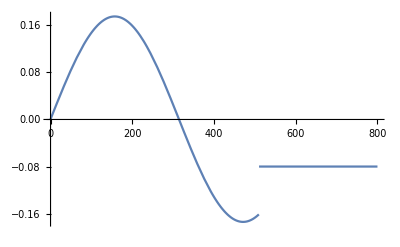

```mathematica
δv[t_]:= Which[
t≤510,10*Degree*(Sin[t/100])+0.0005,
t>510,-0.08]
Plot[Evaluate[δv[t]],{t,0,tf}]
```

```mathematica
δMax=2*Pi;
```

#### Define equations

```mathematica
eqnsDouble[u_,v_,r_,up_,vp_,rp_,ω11_,ω12_,ω21_,ω22_,δv_]:={
Fx21[u,v,r,ω21,up,vp,δv]-Fx22[u,v,r,ω22,up,vp,δv]==0,
ω11-V11w[u,v,r,δv][[1]]/rr1==0,
ω12-V12w[u,v,r,δv][[1]]/rr1==0,
Jz*rp-Nm[u,v,r,up,vp,δv,ω11,ω12,ω21,ω22]==0,
X[u,v,r,δv,ω11,ω12,ω21,ω22,up,vp]-m*ax[up,v,r]==0,
Y[u,v,r,δv,ω11,ω12,ω21,ω22,up,vp]-m*ay[vp,u,r]==0
}/.param
```

#### Initial Conditions

```mathematica
initialConditionsDouble[u_?NumericQ,δv_?NumericQ]:=
FindRoot[{
eqnsDouble[u,v0,r0,0,0,0,ω110,ω120,ω210,ω220,δv]},
{{v0,0.0001},{r0,0.0001},
{ω110,((u/rr1-0.25))},{ω120,((u)/rr1+0.25)},
{ω210,((u)/rr2-0.25)},{ω220,(u/rr2+0.25)}
}/.param
]
```

```mathematica
icDouble=initialConditionsDouble[u[0],δv[0]]
```

{v0→0.0000625654,r0→0.0000473674,ω110→19.9998,ω120→20.0002,ω210→20.0019,ω220→20.0022}

#### NDSolve

```mathematica
message="";
```

```mathematica
DoubleModel[u_,δv_,ts_]:=First@NDSolve[{
eqnsDouble[u,vn[t],rn[t],u'[t],vn'[t],rn'[t],ω11n[t],ω12n[t],ω21n[t],ω22n[t],δv],
vn[0]==v0,
rn[0]==r0,
ω11n[0]==ω110,
ω12n[0]==ω120,
ω21n[0]==ω210,
ω22n[0]==ω220
}/.icDouble,
(*{WhenEvent[Abs@ay[vn'[t],u,rn[t]]≥μ*g/.param,
{"StopIntegration",message="ayMax!"}],
WhenEvent[Abs@δv≥δMax,
{"StopIntegration",message="δMax!"}]},*)
{vn[t],rn[t],ω11n[t],ω12n[t],ω21n[t],ω22n[t]},
{t,0,tf},
AccuracyGoal->8,PrecisionGoal->8
]
```

```mathematica
solDouble=DoubleModel[u[t],δv[t],tf]
```

{vn[t]→InterpolatingFunction[…][t],rn[t]→InterpolatingFunction[…][t],ω11n[t]→InterpolatingFunction[…][t],ω12n[t]→InterpolatingFunction[…][t],ω21n[t]→InterpolatingFunction[…][t],ω22n[t]→InterpolatingFunction[…][t]}

#### State Definition

```mathematica
vD[t_]:=vn[t]/.solDouble;
```

```mathematica
rD[t_]:=rn[t]/.solDouble;
```

```mathematica
ω11D[t_]:=ω11n[t]/.solDouble;
```

```mathematica
ω12D[t_]:=ω12n[t]/.solDouble;
```

```mathematica
ω21D[t_]:=ω21n[t]/.solDouble;
```

```mathematica
ω22D[t_]:=ω22n[t]/.solDouble;
```

```mathematica
ψeqD=NDSolve[{ψsol'[t]==rD[t],ψsol[0]==0},ψsol,{t,0,tf}];
```

```mathematica
ψD[t_]:=First[ψsol[t]/.ψeqD];
```

#### Plot

```mathematica
xgeq=NDSolve[{xgsol'[t]==u[t]*Cos@ψD[t]-vD[t]*Sin@ψD[t],xgsol[0]==0},xgsol,{t,0,tf}];
```

```mathematica
ygeq=NDSolve[{ygsol'[t]==u[t]*Sin@ψD[t]+vD[t]*Cos@ψD[t],ygsol[0]==0},ygsol,{t,0,tf}];
```

```mathematica
xD[t_]:=First[xgsol[t]/.xgeq]
```

```mathematica
yD[t_]:=First[ygsol[t]/.ygeq]
```

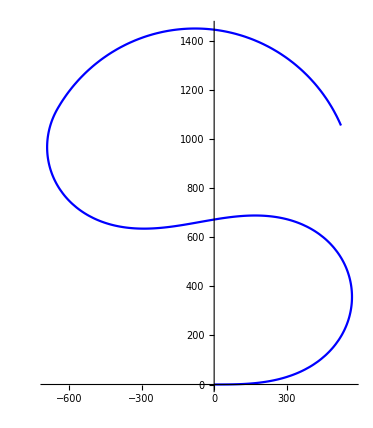

```mathematica
ParametricPlot[
{xD[t],yD[t]},{t,0,tf},
AspectRatio->Automatic,PlotRange->All,
AspectRatio->Automatic,PlotStyle->Blue]
```

```mathematica
Manipulate[
ParametricPlot[{{xD[t],yD[t]}},{t,1,x-1},ImageSize->400],
{x,1,tf,Appearance->"Open",AnimationRate->50}]
```

### Single Track Model

#### Single Track Parameters

```mathematica
dataST={
l->a1+a2,
μ->mu,
qb->((a2*q1+a1*q2)/(a1+a2)),
δ10->0,
δ20->0,
τ1->tau1,τ2->tau2,
ϵ1->0,ϵ2->0,
ρ->rho,
kϕ1->kphi1,kϕ2->kphi2,
kϕ->kphi1+kphi2,
kϕ1p->kphi1p,kϕ2p->kphi2p,
kϕp->kphi1p+kphi2p,
kϕ1s->kphi1s,kϕ2s->kphi2s,
kϕs->kphi1s+kphi2s,
Jz->m*a1*a2*0.92
}/.data;
```

```mathematica
keySingleTrack ={{Key@delta10},{Key@delta20},
{Key@tau1},{Key@tau2},{Key@epsilon1},
{Key@epsilon2}};
```

```mathematica
paramST=Normal@Thread[Delete[Association[Join[data,dataST]],keySingleTrack]];
```

```mathematica
uAC=20;
rAC=1;
vAC=1;
```

#### Compute ΔZi

```mathematica
η1=(ΔZ1[0,uAC,rAC]/Y1[0,uAC,rAC] )*(a2/l);
η2=(ΔZ2[0,uAC,rAC]/Y2[0,uAC,rAC] )*(a1/l);
```

```mathematica
Yi[αij_,ΔZi_,Zi0_]:=
(Ft[αij,Zi0+ΔZi]+Ft[αij,Zi0-ΔZi])/.paramST;
```

```mathematica
computeΔZi[αi_,Zi0_,ai_,ηi_,initCond_]:=
FindRoot[{Yi[αi,ΔZi,Zi0]-(ΔZi*ai)/(ηi*l)}/.paramST,
{ΔZi,initCond},
AccuracyGoal->5,
PrecisionGoal->5]
```

```mathematica
αiAC=Range[-0.2,0.2,0.01];
```

```mathematica
(* Compute ΔZ1 *)
```

```mathematica
ΔZ1AC={};
AppendTo[ΔZ1AC,computeΔZi[αiAC[[1]],Z10,a1,η1,-2000][[1,2]]];
For[i=2,i≤Length@αiAC,i++,
AppendTo[ΔZ1AC,computeΔZi[αiAC[[i]],Z10,a1,η1,ΔZ1AC[[i-1]]][[1,2]]];
]
```

```mathematica
(* Compute ΔZ2 *)
```

```mathematica
ΔZ2AC={};
AppendTo[ΔZ2AC,computeΔZi[αiAC[[1]],Z20,a2,η2,-2000][[1,2]]];
For[i=2,i≤Length@αiAC,i++,
AppendTo[ΔZ2AC,computeΔZi[αiAC[[i]],Z20,a2,η2,ΔZ2AC[[i-1]]][[1,2]]];
]
```

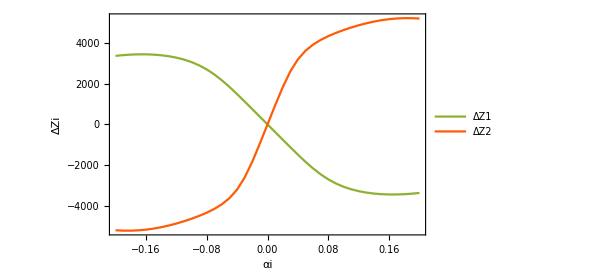

```mathematica
ListLinePlot[{Transpose[{αiAC,ΔZ1AC}],Transpose[{αiAC,ΔZ2AC}]},
PlotRange->All,PlotLegends->{"ΔZ1","ΔZ2"},ImageSize->450,
LabelStyle->Directive[Bold,10],AxesLabel->{"αi","ΔZi"},
PlotStyle->{green,red},Frame->True
]
```

#### Axle Characteristic

```mathematica
Y1AC=Yi[αiAC,ΔZ1AC,Z10]/.paramST;
```

```mathematica
Y2AC=Yi[αiAC,ΔZ2AC,Z20]/.paramST;
```

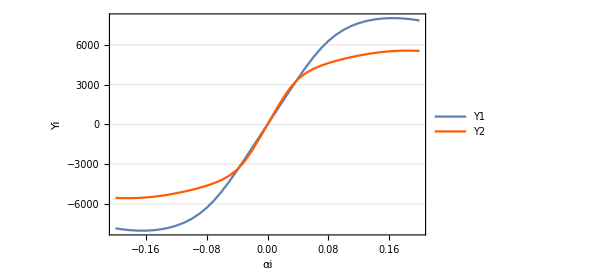

```mathematica
ListLinePlot[{Transpose[{αiAC,Y1AC}],Transpose[{αiAC,Y2AC}]},LabelStyle->Directive[Bold,11],AxesLabel->{"αi","Yi"},
PlotRange->All,PlotLegends->{"Y1","Y2"},ImageSize->450,LabelStyle->Directive[Bold,11],
PlotStyle->{blue,red},Frame->True,GridLines->{None,Automatic},GridLinesStyle->{Dotted,Dotted}]
```

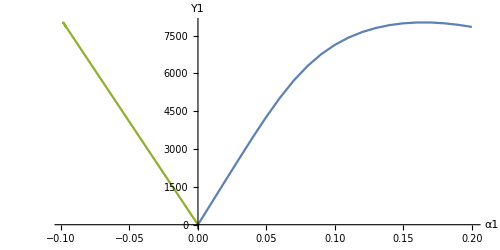

```mathematica
ListLinePlot[{
Transpose[{αiAC[[21;;41]],Y1AC[[21;;41]]}],
Transpose[{ΔZ1AC[[21;;41]]/35000,Y1AC[[21;;41]]}]},
AspectRatio->1/2,ImageSize->500,AxesLabel->{"α1","Y1"},
PlotStyle->{blue,green}]
```

```mathematica
Manipulate[
Column[{
Grid[{{" α1   -> ", αiAC[[x]]},{" ΔZ1  -> ",-ΔZ1AC[[x]]},
{" Y1   -> ",Y1AC[[x]]}},Alignment->Center,Background->{{{None},LightBlue}}],
ListLinePlot[{
Transpose[{αiAC[[21;;41]],Y1AC[[21;;41]]}],
Transpose[{αiAC[[21;;x]],Y1AC[[21;;x]]}],
Transpose[{ΔZ1AC[[21;;41]]/35000,Y1AC[[21;;41]]}],
Transpose[{ΔZ1AC[[21;;x]]/35000,Y1AC[[21;;x]]}]},
AspectRatio->1/2,ImageSize->700,
PlotStyle->{{blue,Dashed,Thickness[0.004]},{Red,Thickness[0.005]} ,
{green,Dashed,Thickness[0.004]},{Red,Thickness[0.005]}},
AxesLabel->{"α1","Y1"},LabelStyle->Directive[Bold,10.6]]}],
{x,21,41,1}]
```

#### SingleTrack Equations

```mathematica
magicFormula=
Dst*Sin[Cst*ArcTan[Bst*x-Est*(Bst*x-ArcTan[Bst*x])]];
```

```mathematica
mf1=FindFit[Transpose[{αiAC,Yi[αiAC,ΔZ1AC,Z10]}]/.paramST,magicFormula,{Bst,Cst,Dst,Est},x]
```

{Bst→7.4721,Cst→1.4809,Dst→7995.19,Est→-1.70226}

```mathematica
mf2=FindFit[Transpose[{αiAC,Yi[αiAC,ΔZ2AC,Z20]}]/.paramST,magicFormula,{Bst,Cst,Dst,Est},x]
```

{Bst→16.8706,Cst→1.05596,Dst→5996.44,Est→0.537587}

```mathematica
Y1SingleTrack[α1_]:=
Dst*Sin[Cst*ArcTan[Bst*α1-Est*(Bst*α1-ArcTan[Bst*α1])]]/.mf1;
```

```mathematica
Y2SingleTrack[α2_]:=
Dst*Sin[Cst*ArcTan[Bst*α2-Est*(Bst*α2-ArcTan[Bst*α2])]]/.mf2;
```

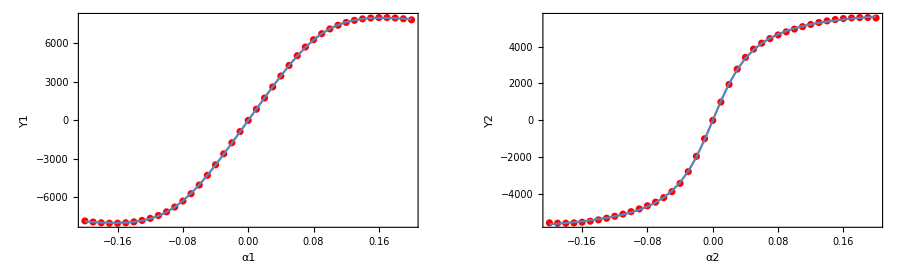

```mathematica
GraphicsRow[ {
Show[ListPlot[{Transpose[{αiAC,Yi[αiAC,ΔZ1AC,Z10]}]},PlotStyle->{Red}],
ListLinePlot[{Transpose[{αiAC,Y1SingleTrack[αiAC]}]}],AxesLabel->{"α1","Y1"},Frame->True],
Show[ListPlot[{Transpose[{αiAC,Yi[αiAC,ΔZ2AC,Z20]}]},PlotStyle->{Red}],
ListLinePlot[{Transpose[{αiAC,Y2SingleTrack[αiAC]}]}],AxesLabel->{"α2","Y2"},Frame->True]
},ImageSize->900]
```

#### Initial Conditions

```mathematica
eqnsSingle[u_,v_,r_,up_,vp_,rp_,ω11_,ω12_,ω21_,ω22_,α1_,α2_,δv_]:={
α1-δv*τ1+(v+r*a1)/u==0,
α2-δv*τ2+(v-r*a2)/u==0,
ω11-V11w[u,v,r,δv][[1]]/rr1==0,
ω12-V12w[u,v,r,δv][[1]]/rr1==0,
Fx21[u,v,r,ω21,up,vp,δv]-Fx22[u,v,r,ω22,up,vp,δv]==0,
X[u,v,r,δv,ω11,ω12,ω21,ω22,up,vp]-m*ax[up,v,r]==0,
Jz*rp-Y1SingleTrack[α1]*a1+Y2SingleTrack[α2]*a2==0,
Y1SingleTrack[α1]+Y2SingleTrack[α2]-m*ay[vp,u,r]==0
}/.paramST
```

```mathematica
tf=800;
```

```mathematica
uM=Interpolation[Drop[Import["Car_Parameters/Gp2_monza_L1.xls",{"Data", 1, All, 3}], 1]]
```

InterpolatingFunction[…]

```mathematica
(*u[t_]:=Piecewise[{{5,0≤t<1},{uM[t],t≥1}}]*)
```

```mathematica
(*δv[t_]:=1*Degree*t*0.3+0.0005*)
```

```mathematica
initialConditionsSingle[u_?NumericQ,δv_?NumericQ]:=
FindRoot[{
eqnsSingle[u,v0,r0,0,0,0,ω110,ω120,ω210,ω220,α10,α20,δv]},
{{v0,0.0001},{r0,0.0001},
{ω110,((u/rr1-0.25))},{ω120,((u)/rr1+0.25)},
{ω210,((u)/rr2-0.25)},{ω220,(u/rr2+0.25)},
{α10,0.001},{α20,0.001}
}/.paramST
]
```

```mathematica
icSingle=initialConditionsSingle[u[0],δv[0]]
```

{v0→0.0000615036,r0→0.0000465551,ω110→19.9999,ω120→20.0001,ω210→20.0019,ω220→20.0022,α10→2.17784×10^-6,α20→1.38647×10^-6}

#### NDSolve

```mathematica
solModelSingle[u_,δv_,ts_]:=First@NDSolve[{
eqnsSingle[u,vn[t],rn[t],u'[t],vn'[t],rn'[t],ω11n[t],ω12n[t],ω21n[t],ω22n[t],α1n[t],α2n[t],δv],
vn[0]==v0,
rn[0]==r0,
ω11n[0]==ω110,
ω12n[0]==ω120,
ω21n[0]==ω210,
ω22n[0]==ω220,
α1n[0]==α10,
α2n[0]==α20
}/.icSingle,
{vn[t],rn[t],ω11n[t],ω12n[t],ω21n[t],ω22n[t],α1n[t],α2n[t]},
{t,0,ts},AccuracyGoal->8,PrecisionGoal->8
]
```

```mathematica
solSingle=solModelSingle[u[t],δv[t],tf];
```

#### State Definition

```mathematica
vS[t_]:=vn[t]/.solSingle;
```

```mathematica
rS[t_]:=rn[t]/.solSingle;
```

```mathematica
ω11S[t_]:=ω11n[t]/.solSingle;
```

```mathematica
ω12S[t_]:=ω12n[t]/.solSingle;
```

```mathematica
ω21S[t_]:=ω21n[t]/.solSingle;
```

```mathematica
ω22S[t_]:=ω22n[t]/.solSingle
```

```mathematica
ψeqS=NDSolve[{ψsol'[t]==rS[t],ψsol[0]==0},ψsol,{t,0,tf}];
```

```mathematica
ψS[t_]:=First[ψsol[t]/.ψeqS];
```

#### Plot

```mathematica
xgeqS=NDSolve[{xgsol'[t]==u[t]*Cos@ψS[t]-vS[t]*Sin@ψS[t],xgsol[0]==0},xgsol,{t,0,tf}];
```

```mathematica
ygeqS=NDSolve[{ygsol'[t]==u[t]*Sin@ψS[t]+vS[t]*Cos@ψS[t],ygsol[0]==0},ygsol,{t,0,tf}];
```

```mathematica
xS[t_]:=First[xgsol[t]/.xgeqS]
```

```mathematica
yS[t_]:=First[ygsol[t]/.ygeqS]
```

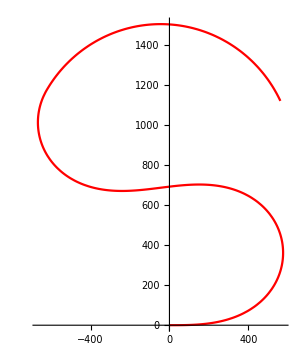

```mathematica
ParametricPlot[{{xS[t],yS[t]}},{t,0,tf},
AspectRatio->Automatic,PlotRange->All,
ImageSize->300,PlotStyle->Red]
```

```mathematica
Manipulate[
ParametricPlot[{{xS[t],yS[t]}},{t,1,x-1},ImageSize->400],
{x,1,tf,Appearance->"Open",AnimationRate->50}]
```

### Comparing

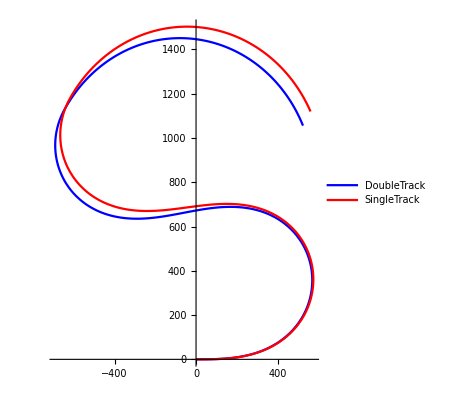

```mathematica
ParametricPlot[{
{xD[t],yD[t]},{xS[t],yS[t]}},{t,0,tf},AspectRatio->Automatic,PlotRange->All,
AspectRatio->Automatic,PlotLegends->{"DoubleTrack","SingleTrack"},
PlotStyle->{Blue,Red}]
```

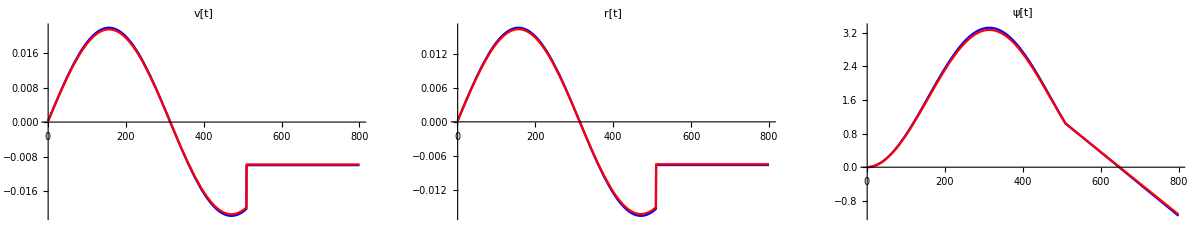

```mathematica
GraphicsRow[{
Plot[{vD[t],vS[t]},{t,1,tf},PlotLabel->"v[t]",PlotStyle->{Blue,Red}],
Plot[{rD[t],rS[t]},{t,1,tf},PlotLabel->"r[t]",PlotStyle->{Blue,Red}],
Plot[{ψD[t],ψS[t]},{t,1,tf},PlotLabel->"ψ[t]",PlotStyle->{Blue,Red}]},
ImageSize->1200,Frame->True,PlotLabel->"Comparison of Single and Double Track Model"]
```